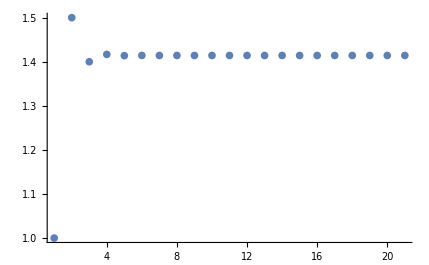

```mathematica
values = RecurrenceTable[{x[n+1] == x[n]+2y[n],y[n+1]==x[n]+y[n],x[0]==1,y[0]==1},{x,y},{n,0,20}];
xs = Apply[Divide, values, {1}];
ListPlot[xs, PlotRange->All]
```

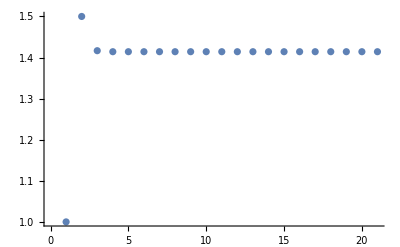

```mathematica
f[x_]=x^2-2;
ListPlot[NestList[#-f[#]/f'[#] &, 1, 20]]
```

```mathematica
FindRoot[x^2-2==0, {x,0,20}]
```

{x→1.41421}

```mathematica
g[f_,x0_]:=FixedPoint[#-f[#]/f'[#]&,x0]
g[#^2-2&,1.0]
```

1.41421